# Simulation of the max stationary values inDirected Configuration Model (DCM) with power-law in-degree distribution

## Setup

Load the package for simulation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<DCM`
```

File name of the simulation result data

```mathematica
datafile="max-stationary-data.wl"
```

max-stationary-data.wl

The range of the size of graphs

```mathematica
nmin=1000;nmax=10^4+1000;nstep=2*10^3;
```

```mathematica
nlist=Range[nmin,nmax,nstep]
```

{1000,3000,5000,7000,9000,11000}

```mathematica
a0=5/2;r0=2;
```

Where to cut-off max degree.

```mathematica
p0=1/2;
```

Teleporting probability

```mathematica
a1=1/4;
```

## Degree sequences

## The limit distribution of in-degrees

We will simulate DCM with out-degree fixed to be r0 and in-degree with limit distribution

```mathematica
dist=heavyTailDist[a0,r0]
```

ProbabilityDistribution[Piecewise[{{2/(x^(7/2) (-1+Zeta[5/2])), x≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), x==0}, {0, True}}],{x,0,∞,1}]

The PDF of this distribution

```mathematica
pdf[i_]=PDF[dist,i]
```

Piecewise[{{2/(i^(7/2) (-1+Zeta[5/2])), i≥2}, {(1+Zeta[5/2]-2 Zeta[7/2])/(-1+Zeta[5/2]), i==0}, {0, True}}]

Moments

```mathematica
Moment[dist,1]
```

2

```mathematica
Moment[dist,2]//N
```

9.44325

## The actual bi-degree sequence

Since dist is only a limit, we have create degree sequence which are approximately distributed like it for the simulation.

And we have to decide the max degree for each n. The parameter p0 controls where to cutoff.

```mathematica
deglistlist=Table[pdf2Deg[pdf,r0,nn,p0],{nn,nmin,nmax,nstep}];
```

We draw some pictures of the in-degrees

```mathematica
histlist=(Histogram[#1⟦1⟧,{0,10,1},"Probability",ImageSize->Medium]&)/@deglistlist;
```

```mathematica
p2=DiscretePlot[pdf[i],{i,0,10,1},PlotRange->Full];
```

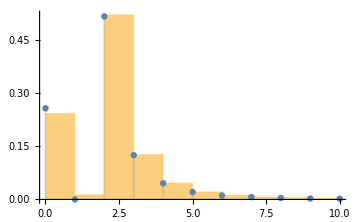
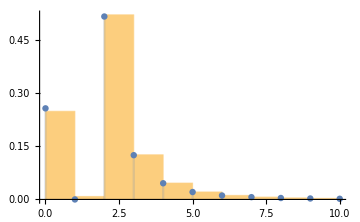
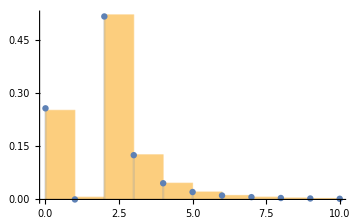
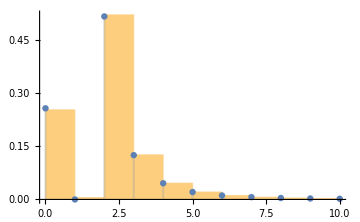
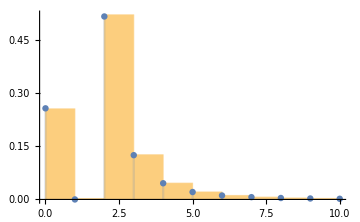
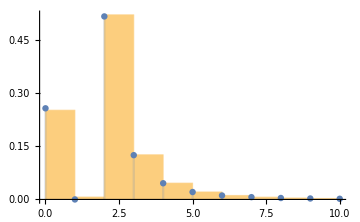

```mathematica
Show[#,p2]&/@histlist
```

As can be seen from the pictures, these degree sequences dos approximates the limit distribution.

## The maximum degrees

The max degrees for each n are

```mathematica
maxdlist=deglistlist[[;;,1,-1]]
```

{15,20,24,26,28,29}

So the max degree grows approximately as

```mathematica
data1=Transpose[{maxdlist,nlist}];
```

```mathematica
fit=Fit[data1,{n^(a0+1)},n]
```

0.0798118 n^(7/2)

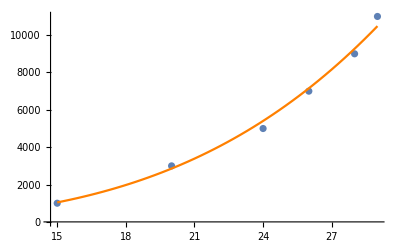

```mathematica
Show[ListPlot[data1],Plot[fit,{n,maxdlist⟦1⟧,maxdlist⟦-1⟧},PlotStyle->Orange,ImageSize->Large]]
```

## Simulation

Warning: This part may take very long time to run.

We will simulate DCM of different sizes and collect data of the maximum stationary distribution and the stationary distribution of the node with max degree.

The number of samples for each n

```mathematica
nsample0=500;
```

```mathematica
Clear[data]
```

```mathematica
data=Monitor[Table[simDCM[pdf,r0,n,p0,a1,nsample0],{n,nmin,nmax, nstep}],n];
```

Save the data to a file.

```mathematica
DeleteFile[datafile]//Quiet;
```

```mathematica
Save[datafile,data]
```

## Analysis

Load simulation data.

```mathematica
Clear[data]
```

```mathematica
Get[datafile];
```

Simulation result is as follows. The column piDelta is the average stationary value of the node with max in-degree Δ^-. The column pimax is the average max stationary value.

```mathematica
<<DCM`
```

```mathematica
result=Dataset[simAnalyze/@data]
```

We see that piDelta is more or less Δ^-/m, while the pimax is larger by a constant factor of about 1.3.

```mathematica
col={"pimax/(Δ/m)","piDelta/(Δ/m)","prmax/(Δ/m)","prDelta/(Δ/m)"};
```

```mathematica
result[[1]][col]
```

```mathematica
Table[Head[row],{row, Normal[result]}]
```

{Association,Association,Association,Association,Association,Association}

This can also be seen from the picture.

```mathematica
<<MaTeX`
points=With[{row=#},({row["n"],row[#]})&/@col]&/@result//Normal//Transpose;
```

```mathematica
legends=(MaTeX[#,Magnification->2]&/@{"\\frac{\\pi_{\\max}}{\\Delta^{-}/m}","\\frac{\\pi_{\\Delta^{-}}}{\\Delta^{-}/m}","\\frac{\\mathrm{PR}_{\\max}}{\\Delta^{-}/m}","\\frac{\\mathrm{PR}_{\\Delta^{-}}}{\\Delta^{-}/m}"});
```

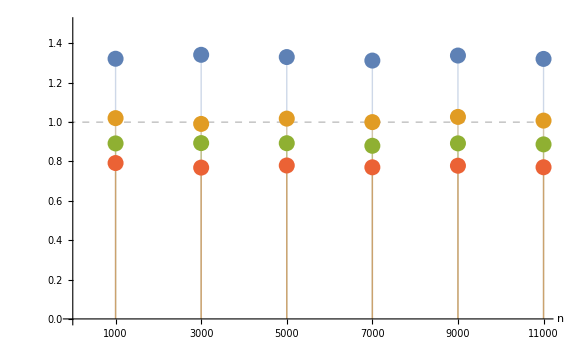

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
plt=ListPlot[points,BaseStyle->texStyle,PlotRange->{0,1.5},Filling->Axis,ImageSize->Large,AxesLabel->{"n",None},GridLines->{{}, {1}},PlotLegends->legends,GridLinesStyle->Directive[Thick,Gray, Dashed],PlotStyle->PointSize[0.02],Ticks->{nlist, Automatic}]
```

```mathematica
Export["simulation.pdf",plt];
```

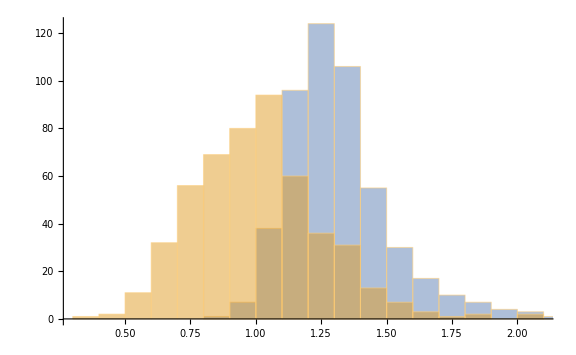
-Graphics--Graphics-

```mathematica
h1=Labeled[Histogram[#["hist"],BaseStyle->texStyle,ImageSize->Large,ChartLegends->legends,ChartStyle->ColorData[97,"ColorList"]],MaTeX[StringForm["n=``",#["n"]],Magnification->2]]& @ result[[-1]]
```

```mathematica
Export["hist.pdf",h1];
```